xa = 1.21489, xb = 25.0893

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.37294} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.76606} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

xf = 14.4576(16.4404), xa = 1.21489(195.646), xb = 25.0893(9.47367)

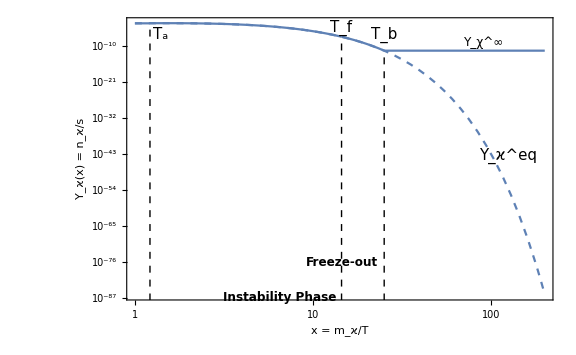

```mathematica
Clear[Ychi,x,xa,xb,xf,mchi,sfsi]

Mp=2.435*10^18;
hbar=6.58*10^(-25);
c=3*10^8;
mt=160;
mW=80.385;
mZ=91.2;
GF=1.166378 10^-5;
v=1/Sqrt[Sqrt[2]*GF];
alphaem=1/128;
sw2=0.23129;
mh=125;
h=0.673;
kB=8.6173303 10^-5*10^-9 ; (* GeV/K*)
T0=kB*2.7255;
H0=(0.678 * hbar)/(9.777752 10^9 * 365.25*24*3600);
s0=4/3 π^2/30(2+21/11)T0^3;
g=Sqrt[8/Sqrt[2] GF*mW^2];
gprime=Sqrt[(4 π *alphaem)/(1-sw2)];

yt=Sqrt[2]*(mt/v);

lambda1=mh^2/v^2;
lambda2=0.8294;
lambda3=2.7709;
lambda4=0.2153;
lambda5=-0.0303;
l345=lambda3+lambda4+lambda5;

c1=(3*lambda1+2*lambda3+lambda4)/12+(3*g^2+gprime^2)/32+yt^2/8;
c2=(3*lambda2+2*lambda3+lambda4)/12+(3*g^2+gprime^2)/32;

mchi=237.6881;
Metapm=264.5752;

muH2=lambda1*v^2;
mueta2=lambda3*v^2-2*Metapm^2;
MetaR2=Metapm^2+(lambda4+lambda5)*(v^2/2);
MetaI2=Metapm^2+(lambda4-lambda5)*(v^2/2);

xa=(Sqrt[c2]*mchi)/Sqrt[mueta2];
xb=Sqrt[(Sqrt[lambda2]*c1*mchi^2-Sqrt[lambda1]*c2*mchi^2)/(Sqrt[lambda2]*muH2-Sqrt[lambda1]*mueta2)];

Print["xa = ",xa,", xb = ",xb]

(*Masses non-rel at xb - True*)

MetaR2>(mchi/xb)^2;
MetaI2>(mchi/xb)^2;
mW^2 > (mchi/xb)^2;
mZ^2 > (mchi/xb)^2;

(*...........*)

Yalpha2=1.7*10^(-7);

sigmavchi=(1/(4*Pi*mchi^2))*Yalpha2^2;
Gammachi=(3*mchi/(32*Sqrt[2]*Pi))*Yalpha2;

gchi=2;
gstar=100;
Hchi=Sqrt[Pi^2*gstar/90]*(mchi^2/Mp);
schi=(2*Pi^2*gstar/45)*mchi^3;

lambdachi=(schi*sigmavchi)/Hchi//N;

Omegachih2=0.112;
Yinf=(3*H0^2*Mp^2*Omegachih2)/(mchi*s0*h^2) ;

sfsi[x_]:=1+0.006*(100/gstar)*(c1*mueta2-c2*muH2)/(Sqrt[lambda1*lambda2]*(mchi/x));

Ychieq[x_]:=(45/(2*Pi^4))*(Pi/8)^(1/2)*(gchi/gstar)*x^(3/2)*Exp[-x];

solxb=Solve[Ychieq[x]/sfsi[x]==Yinf,x];

xmin=1;
xa=xa;
xb=xb;
xmax=100;

sol1=NDSolve[{Ychi'[x]==-(lambdachi/x^2)*(Ychi[x]^2-Ychieq[x]^2),Ychi[xmin]==Ychieq[xmin]},Ychi,{x,xmin,xa}];
sol2=NDSolve[{Ychi'[x]==-(Gammachi*x/Hchi)*(Ychi[x]-Ychieq[x])-(lambdachi/x^2)*(Ychi[x]^2-Ychieq[x]^2),Ychi[xa]==(Ychi[xa]/.sol1[[1]])},Ychi,{x,xa,xb}];
sol3=NDSolve[{Ychi'[x]==-(lambdachi/x^2)*(Ychi[x]^2-Ychieq[x]^2),Ychi[xb]==(Ychi[xb]/.sol2[[1]])},Ychi,{x,xb,xmax}];

Ploteq=LogLogPlot[Ychieq[x],{x,xmin,200},PlotRange->All,PlotStyle->Dashed,Axes->False];
Plot1=LogLogPlot[Ychi[x]/.sol1,{x,xmin,xa},PlotRange->All,Axes->False];
Plot2=LogLogPlot[Ychi[x]/.sol2,{x,xa,xb},PlotRange->All];
Plot3=LogLogPlot[Ychi[x]/.sol3,{x,xb,xmax},PlotRange->All];

(* Find xf *)

s[x_]:=(2*Pi^2*gstar/45)*(mchi/x)^3
H[x_]:=Sqrt[Pi^2*gstar/90]*(mchi^2/(Mp*x^2));
Plot[H[x]-sigmavchi*s[x]*(Ychi[x]/.sol1),{x,1,50}];
xf=x/.FindRoot[H[x]-sigmavchi*s[x]*(Ychi[x]/.sol1)==0,{x,1.5}];

Print["xf = ",xf,"(",mchi/xf,")",", xa = ",xa,"(",mchi/xa,")", ", xb = ",xb,"(",mchi/xb,")"]

sole1=NDSolve[{Ychi'[x]==-(lambdachi/x^2)*(Ychi[x]^2-Ychieq[x]^2),Ychi[xmin]==Ychieq[xmin]},Ychi,{x,xmin,xa}]; (* up to xa *)

delta1[x_]=-D[Ychieq[x],x]/((Gammachi/Hchi)*x+(2*lambdachi/x^2)*Ychieq[x]);
delta2[x_]=-D[Ychieq[x],x]/((Gammachi/Hchi)*x);

Ychie1[x_]=Ychieq[x]+delta1[x]; (* xa -> xf *)
Ychie2[x_]=Ychieq[x]+delta2[x]; (* xf -> xb *)

Ychiinfe[x_]=(Ychieq[xb]*xb)/(Ychieq[xb]*lambdachi+xb); (* xb -> Infinity *)

Ploteq=LogLogPlot[Ychieq[x],{x,xmin,200},PlotRange->All,PlotStyle->Dashed,Axes->False];
Plote1=LogLogPlot[Ychi[x]/.sole1,{x,xmin,xa},PlotRange->All,Axes->False];
Plote2=LogLogPlot[Ychie1[x],{x,xa,xf},PlotRange->All,Axes->False];
Plote3=LogLogPlot[Ychie2[x],{x,xf,xb},PlotRange->All,Axes->False];
Plote4=LogLogPlot[Ychiinfe[x],{x,xb,200},PlotRange->All,Axes->False];

Line1=Line[{{Log[xa],-1000},{Log[xa],Log[Ychieq[xa]]}}];
Line2=Line[{{Log[xf],-1000},{Log[xf],Log[Ychie1[xf]]}}];
Line3=Line[{{Log[xb],-1000},{Log[xb],Log[Ychie2[xb]]}}];

Show[Ploteq,Plote1,Plote2,Plote3,Plote4,PlotRange->All,Frame->{True,True,True,True},FrameLabel->{{"Y_ϰ(x) = n_ϰ/s",""},{"x = m_ϰ/T",""}},FrameTicks->{0},LabelStyle->Directive[Bold,15],ImageSize->Large,Epilog->{Directive[{Dashed}],Line1,Line2,Line3,Text[Style["T_a",15],{1.7*Log[xa],-15}],Text[Style["T_f",15],{Log[xf],-10}],Text[Style["T_b",15],
{Log[xb],-15}],Text[Style["Y_ϰ^eq",15],{1.5*Log[xb],-100}],
Text[Style["Y_χ^∞",12],{1.4*Log[xb],-20}],Text[Style["Instability Phase",12,Bold],{0.7*Log[xf],-200}],Text[Style["Freeze-out",12,Bold],{Log[xf],-175}]}]
Show[Ploteq,Plote1,Plote2,Plote3,Plote4,PlotRange->All,Frame->{True,True,True,True},FrameLabel->{{"Y_ϰ(x) = n_ϰ/s",""},{"x = m_ϰ/T",""}},FrameTicks->{0},LabelStyle->Directive[Bold,15],ImageSize->Large,Epilog->{Directive[{Dashed}],Line1,Line2,Line3,Text[Style["T_a=196 GeV",12],{3*Log[xa],-15}],Text[Style["T_f=16.4 GeV",12],{1.05*Log[xf],-10}],Text[Style["T_b=9.5 GeV",12],
{1.05*Log[xb],-20}],Text[Style["Y_ϰ^eq",15],{1.5*Log[xb],-100}],
Text[Style["Ω_χh^2~0.1",12],{1.4*Log[xb],-20}],Text[Style["Instability Phase",12,Bold],{0.7*Log[xf],-200}],Text[Style["Freeze-out",12,Bold],{Log[xf],-175}]}]
```

```mathematica
Clear[Ychi,x,xa,xb,xf,mchi,sfsi]

Mp=2.435*10^18;
hbar=6.58*10^(-25);
c=3*10^8;
mt=160;
mW=80.385;
mZ=91.2;
GF=1.166378 10^-5;
v=1/Sqrt[Sqrt[2]*GF];
alphaem=1/128;
sw2=0.23129;
mh=125;
h=0.673;
kB=8.6173303 10^-5*10^-9 ; (* GeV/K*)
T0=kB*2.7255;
H0=(0.678 * hbar)/(9.777752 10^9 * 365.25*24*3600);
s0=4/3 π^2/30(2+21/11)T0^3;
g=Sqrt[8/Sqrt[2] GF*mW^2];
gprime=Sqrt[(4 π *alphaem)/(1-sw2)];

yt=Sqrt[2]*(mt/v);

lambda1=mh^2/v^2;
lambda2=0.8294;
lambda3=2.7709;
lambda4=0.2153;
lambda5=-0.0303;
l345=lambda3+lambda4+lambda5;

c1=(3*lambda1+2*lambda3+lambda4)/12+(3*g^2+gprime^2)/32+yt^2/8;
c2=(3*lambda2+2*lambda3+lambda4)/12+(3*g^2+gprime^2)/32;

mchi=100;
Metapm=200;

muH2=lambda1*v^2;
mueta2=lambda3*v^2-2*Metapm^2;
MetaR2=Metapm^2+(lambda4+lambda5)*(v^2/2);
MetaI2=Metapm^2+(lambda4-lambda5)*(v^2/2);

xa=(Sqrt[c2]*mchi)/Sqrt[mueta2];
xb=Sqrt[(Sqrt[lambda2]*c1*mchi^2-Sqrt[lambda1]*c2*mchi^2)/(Sqrt[lambda2]*muH2-Sqrt[lambda1]*mueta2)];

xa = 1000;
xb = xa+50;

Mp=10^15;

Yalpha2=1*10^(-5);

sigmavchi=(1/(4*Pi*mchi^2))*Yalpha2^2;
Gammachi=(3*mchi/(32*Sqrt[2]*Pi))*Yalpha2;

gchi=2;
gstar=100;
Hchi=Sqrt[Pi^2*gstar/90]*(mchi^2/Mp);
schi=(2*Pi^2*gstar/45)*mchi^3;

lambdachi=(schi*sigmavchi)/Hchi//N;

Ychieq[x_]:=(45/(2*Pi^4))*(Pi/8)^(1/2)*(gchi/gstar)*x^(3/2)*Exp[-x];

xmin=1;
xa=xa;
xb=xb;
xmax=500;

sol1=NDSolve[{Ychi'[x]==-(lambdachi/x^2)*(Ychi[x]^2-Ychieq[x]^2),Ychi[xmin]==Ychieq[xmin]},Ychi,{x,xmin,xa}]; (* up to xa *)

Yxa=Ychi[xa]/.sol1[[1]];

Ychi1[x_]=Yxa*Exp[-(1/gchi)*(Gammachi/Hchi)*(x^2-xa^2)]/(1+lambdachi*Yxa*((gchi*Hchi)/(2*Gammachi))*(1/xa^3-Exp[-(1/gchi)*(Gammachi/Hchi)*(x^2-xa^2)]/x^3))

Ploteq=LogLogPlot[Ychieq[x],{x,xmin,600},PlotRange->All,PlotStyle->Dashed,Axes->False];
Plot1=LogLogPlot[Ychi[x]/.sol1,{x,xmin,xa},PlotRange->All,Axes->False];
Plot2=LogLogPlot[Ychi1[x],{x,xa,xb},PlotRange->All,Axes->False];
Plot3=LogLogPlot[Ychi1[xb],{x,xb,10000},PlotRange->All,Axes->False]

Line1=Line[{{Log[xa],-1000},{Log[xa],Log[Ychieq[xa]]}}];
Line3=Line[{{Log[xb],-1000},{Log[xb],Log[Ychi1[xb]]}}];

Show[Ploteq,Plot1,Plot2,Plot3,PlotRange->All,Frame->{True,True,True,True},FrameLabel->{{"Y_ϰ(x) = n_ϰ/s",""},{"x = m_ϰ/T",""}},FrameTicks->{0},LabelStyle->Directive[Bold,15],Epilog->{Directive[{Dashed}],Text[Style["x_a",15],{2*Log[xa],-15}],Text[Style["x_f",15],{Log[xa],-5}],Text[Style["x_b",15],
{Log[xb],-10}],Text[Style["Y_ϰ^eq",15],{1.5*Log[xb],-85}],
Text[Style["Ω_χh^2~0.1",12],{1.4*Log[xb],-15}]}]
```